## Hayes & Adams (2017) Mathematica Notebook 4 Monte Carlos & Model Projections for the MYTH Model

This document is a pdf created from a Wolfram Mathematica notebook prepared by Mark A. Hayes during December 2016, following the general approach for logistic regression and Monte Carlo simulations outlined in Hayes (2011). This code and output supports the analysis described in Hayes, M. A. and R. A. Adams. 2017. Simulated bat populations collapse when exposed to conditions that mimic climate change projections for western North America. PLOS ONE. If you would like a copy of the original Mathematica notebook, please contact MAH at hayesm@usgs.gov or hayes.a.mark@gmail.com.  

This uses the model Temp + Precip with beta estimates from the full model. 

Mark A. Hayes
January 10, 2017

### Set the directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

\\IGSKBACBFS2\groups\bts\t\mah\manuscripts\2016\Hayes & Adams 2016 - Bat pop modeling - PLOS ONE\revision - fall winter 2016\Plos One - Data package

#### Deterministic repro rate = 0.85

```mathematica
DetRepro = {0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85};
```

## Current Climate 1950-2000 Projections and Simulations

### Model projections using current climate average values

Predicted probability of an adult female being reproductively active in a given year, given RCP26 average values for years 2009-2086, using logistic regressiion.

```mathematica
ProbCurrentAve = {0.8500,0.8480,0.8459,0.8439,0.8419,0.8399,0.8378,0.8358,0.8338,0.8318,0.8297,0.8277,0.8257,0.8237,0.8216,0.8196,0.8176,0.8155,0.8135,0.8115,0.8095,0.8074,0.8054,0.8034,0.8014,0.7993,0.7973,0.7953,0.7933,0.7912,0.7892,0.7872,0.7851,0.7831,0.7811,0.7791,0.7770,0.7750,0.7730,0.7710,0.7689,0.7669,0.7649,0.7629,0.7608,0.7588,0.7568,0.7547,0.7527,0.7507,0.7487,0.7466,0.7446,0.7426,0.7406,0.7385,0.7365,0.7345,0.7325,0.7304,0.7284,0.7264,0.7243,0.7223,0.7203,0.7183,0.7162,0.7142,0.7122,0.7102,0.7081,0.7061,0.7041,0.7021,0.7000,0.6980,0.6960,0.6939};
Mean[ProbCurrentAve]
```

0.771973

```mathematica
aReproCurrentAve =ProbCurrentAve;
```

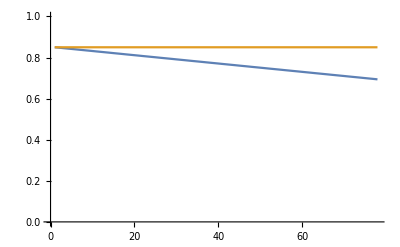

```mathematica
ListLinePlot[{aReproCurrentAve, DetRepro},PlotRange->{0,1}]
```

### Monte Carlo RCP 26 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproCurrentAve/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproCurrentAve/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

396.382

82.3995

182.

815.

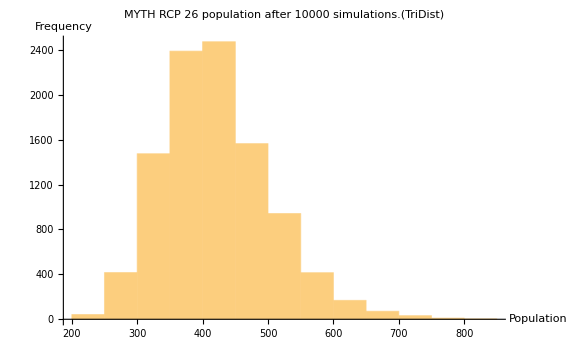

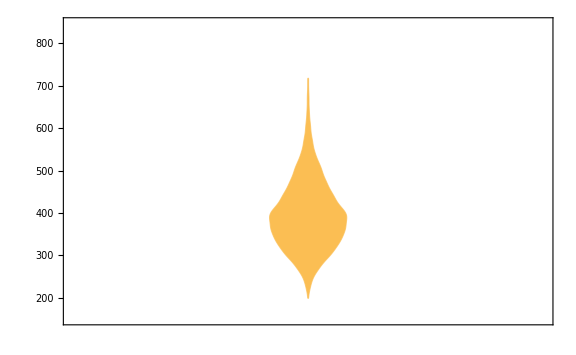

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 26 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```

## RCP 2.6 Projections and Simulations

### Model projections using RCP26 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP26 average values for years 2009-2086, using logistic regressiion.

```mathematica
ProbRCP26Ave = {0.8500,0.8466,0.8431,0.8397,0.8362,0.8328,0.8293,0.8259,0.8225,0.8190,0.8156,0.8121,0.8087,0.8052,0.8018,0.7984,0.7949,0.7915,0.7880,0.7846,0.7811,0.7777,0.7743,0.7708,0.7674,0.7639,0.7605,0.7570,0.7536,0.7502,0.7467,0.7433,0.7398,0.7364,0.7330,0.7295,0.7261,0.7226,0.7192,0.7157,0.7123,0.7089,0.7054,0.7020,0.6985,0.6951,0.6916,0.6882,0.6848,0.6813,0.6779,0.6744,0.6710,0.6675,0.6641,0.6607,0.6572,0.6538,0.6503,0.6469,0.6434,0.6400,0.6366,0.6331,0.6297,0.6262,0.6228,0.6193,0.6159,0.6125,0.6090,0.6056,0.6021,0.5987,0.5952,0.5918,0.5884,0.5849};
Mean[ProbRCP26Ave]
```

0.717459

```mathematica
aReproRCP26Ave =ProbRCP26Ave;
```

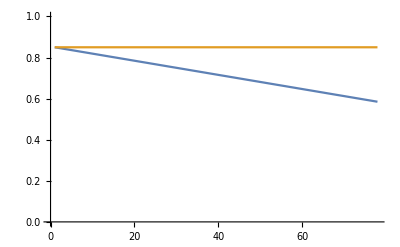

```mathematica
ListLinePlot[{aReproRCP26Ave, DetRepro},PlotRange->{0,1}]
```

### Monte Carlo RCP 26 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP26Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP26Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

125.885

26.9652

61.

267.

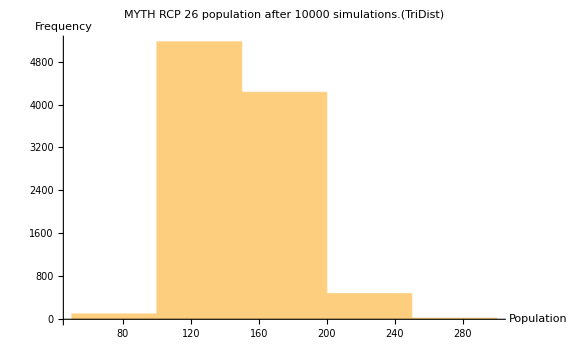

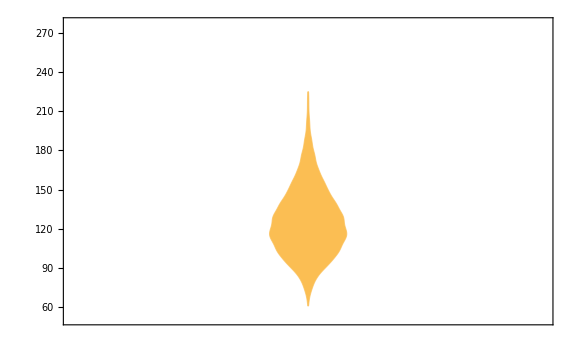

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 26 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```

## RCP 4.5 Projections and Simulations

### Model projections using RCP45 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP45 average values for years 2009-2086, using logistic regression.

```mathematica
ProbRCP45Ave = {0.8500,0.8458,0.8415,0.8373,0.8331,0.8289,0.8246,0.8204,0.8162,0.8119,0.8077,0.8035,0.7992,0.7950,0.7908,0.7866,0.7823,0.7781,0.7739,0.7696,0.7654,0.7612,0.7570,0.7527,0.7485,0.7443,0.7400,0.7358,0.7316,0.7273,0.7231,0.7189,0.7147,0.7104,0.7062,0.7020,0.6977,0.6935,0.6893,0.6850,0.6808,0.6766,0.6724,0.6681,0.6639,0.6597,0.6554,0.6512,0.6470,0.6428,0.6385,0.6343,0.6301,0.6258,0.6216,0.6174,0.6131,0.6089,0.6047,0.6005,0.5962,0.5920,0.5878,0.5835,0.5793,0.5751,0.5709,0.5666,0.5624,0.5582,0.5539,0.5497,0.5455,0.5412,0.5370,0.5328,0.5286,0.5243};
Mean[ProbRCP45Ave]
```

0.687164

```mathematica
aReproRCP45Ave =ProbRCP45Ave;
```

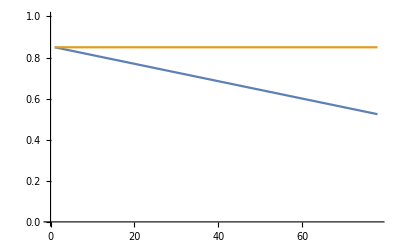

```mathematica
ListLinePlot[{aReproRCP45Ave, DetRepro},PlotRange->{0,1}]
```

### Monte Carlo RCP 45 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP45Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP45Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

66.5271

14.5714

29.

144.

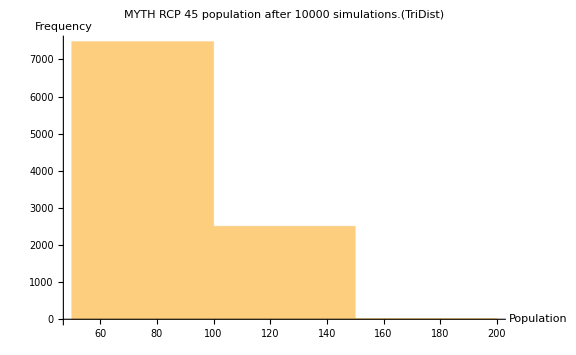

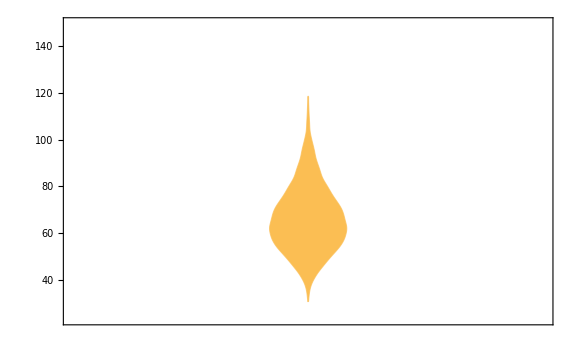

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 45 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```

## RCP 6.0

### Model projections using RCP60 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP60 average values for years 2009-2086, using logistic regression:
Average RCP60 values for years 2009-2086 (from 1995, substract 15):

```mathematica
ProbRCP60Ave = {0.8500,0.8458,0.8415,0.8373,0.8331,0.8289,0.8246,0.8204,0.8162,0.8119,0.8077,0.8035,0.7992,0.7950,0.7908,0.7866,0.7823,0.7781,0.7739,0.7696,0.7654,0.7612,0.7570,0.7527,0.7485,0.7443,0.7400,0.7358,0.7316,0.7273,0.7231,0.7189,0.7147,0.7104,0.7062,0.7020,0.6977,0.6935,0.6893,0.6850,0.6808,0.6766,0.6724,0.6681,0.6639,0.6597,0.6554,0.6512,0.6470,0.6428,0.6385,0.6343,0.6301,0.6258,0.6216,0.6174,0.6131,0.6089,0.6047,0.6005,0.5962,0.5920,0.5878,0.5835,0.5793,0.5751,0.5709,0.5666,0.5624,0.5582,0.5539,0.5497,0.5455,0.5412,0.5370,0.5328,0.5286,0.5243};
Mean[ProbRCP60Ave]
```

0.687164

```mathematica
aReproRCP60Ave =ProbRCP60Ave;
```

```mathematica
ListLinePlot[{aReproRCP60Ave,DetRepro},PlotRange->{0,1}]
```

-Graphics-

### Monte Carlo RCP 60 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP60Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP60Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

66.4887

14.5704

28.

148.

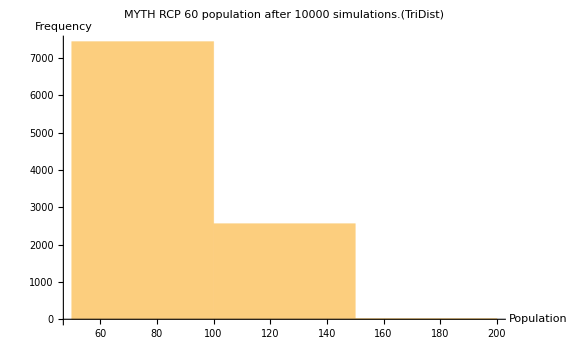

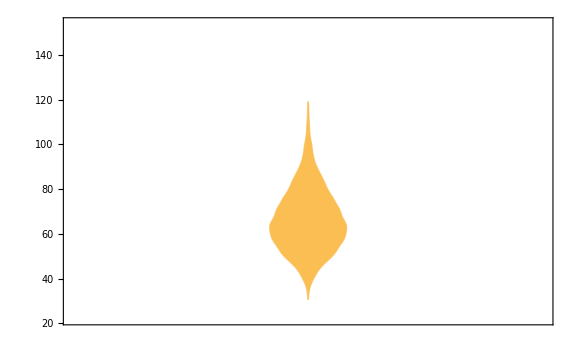

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 60 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```

## RCP 8.5

### Model projections using RCP85 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP85 average values for years 2009-2086, using logistic regression:
Average RCP85 values for years 2009-2086 (from 1995, substract 15):

```mathematica
ProbRCP85Ave = {0.8500,0.8446,0.8392,0.8338,0.8284,0.8230,0.8175,0.8121,0.8067,0.8013,0.7959,0.7905,0.7851,0.7797,0.7743,0.7689,0.7634,0.7580,0.7526,0.7472,0.7418,0.7364,0.7310,0.7256,0.7202,0.7148,0.7093,0.7039,0.6985,0.6931,0.6877,0.6823,0.6769,0.6715,0.6661,0.6607,0.6552,0.6498,0.6444,0.6390,0.6336,0.6282,0.6228,0.6174,0.6120,0.6066,0.6011,0.5957,0.5903,0.5849,0.5795,0.5741,0.5687,0.5633,0.5579,0.5525,0.5470,0.5416,0.5362,0.5308,0.5254,0.5200,0.5146,0.5092,0.5038,0.4984,0.4930,0.4875,0.4821,0.4767,0.4713,0.4659,0.4605,0.4551,0.4497,0.4443,0.4389,0.4334};
Mean[ProbRCP85Ave]
```

0.641723

```mathematica
aReproRCP85Ave =ProbRCP85Ave;
```

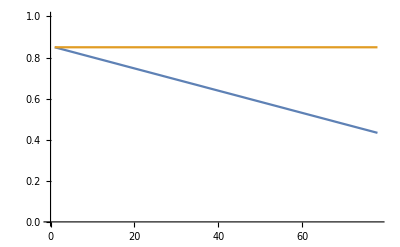

```mathematica
ListLinePlot[{aReproRCP85Ave, DetRepro},PlotRange->{0,1}]
```

### Monte Carlo RCP 85 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP85Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP85Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

25.8041

5.79915

10.

70.

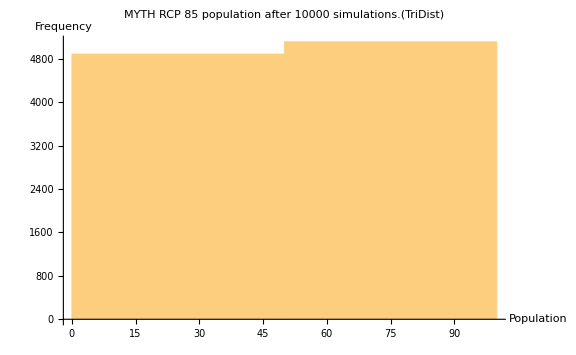

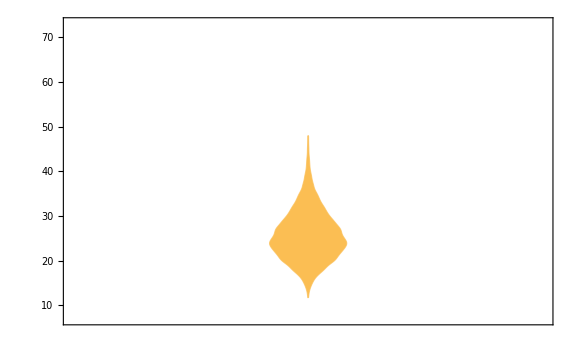

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 85 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```